## Stochastic Variational Method

This notebook aims to find a precise upper bound on the binding energy of n particles interacting via pairwise potentials.  It relies heavily on the formulas presented in “Stochastic Variational Approach to Quantum-Mechanical Few-Body Problems” by Suzuki and Varga. It maintains units in a.u., where unity is m_e, e (charge), k_e, and ℏ.

Input parameters

```mathematica
(* Number of Particles *)
n=4;
(* List of masses of each particle *)
mlist = {1,1,1,1};
ℏ=1;
```

Jacobi matrices and other important linear transforms

```mathematica
(* Coordinate transform matrices: U and U^-1 on p. 10 *)
U=Table[ If[i ≤  j,
mlist[[i]]/Sum[mlist[[k]],{k,1,j}], If[ i -1==j, -1, 0]],{j,n-1},{i,n}];
Uinv = Table[ If[i ≥  j,
mlist[[i+1]]/Sum[mlist[[k]],{k,1,i+1}], If[ i==j - 1, (-Sum[mlist[[k]],{k,1,j-1}])/Sum[mlist[[k]],{k,1,j}], 0]],{j,n},{i,n-1}];
```

```mathematica
(* Coordinate transform matrix p. 11 *)
Λ=Table[Sum[1/mlist[[k]] U[[i,k]]*U[[j,k]],{k,n}],{i,n-1},{j,n-1}];
```

```mathematica
(* Coordinate transform matrix p. 11 *)
w[i_,j_]:=Table[Uinv[[i,k]]-Uinv[[j,k]],{k,n-1}]
```

### Symmetrization matrices

```mathematica
(* Symmetrization matrices p. 16. The matrices for n=3 are given below *)
Tp23 = Table[U[[i,1]]*Uinv[[1,j]]+U[[i,2]]Uinv[[3,j]]+U[[i,3]]Uinv[[2,j]],{j,n-1},{i,n-1}];
Tp13=Table[U[[i,1]]*Uinv[[3,j]]+U[[i,2]]Uinv[[2,j]]+U[[i,3]]Uinv[[1,j]],{j,n-1},{i,n-1}];
Tp12=Table[U[[i,1]]*Uinv[[2,j]]+U[[i,2]]Uinv[[1,j]]+U[[i,3]]Uinv[[3,j]],{j,n-1},{i,n-1}];
```

```mathematica
(* Matrices used in symmetrization, below is ex: three identical fermions *)
tpsOps={#&,
Transpose[Tp13].#.(Tp13)&,
Transpose[Tp12].#.Tp12&,
Transpose[Tp12.Tp13].#.(Tp12.Tp13)&};
```

```mathematica
(* coefficients on the terms in list above *)
opCoef={1,-1,1,-1};
```

```mathematica
(* Operator to distribute Tps over in the calculations, produces list of all multiplications in distribution *)
tpsoped[X_,Y_]=Flatten[Table[{a @X, b @Y},{a,tpsOps},{b,tpsOps}],1];
```

```mathematica
prodOpCoef=Flatten[Table[a*b,{a,opCoef},{b,opCoef}],1];
```

Matrix Elements and Symmetrization

Overlap Matrix

```mathematica
(* Formula eq. 7.4 on p. 127 *)
Bprod[X_,Y_]:=((2π)^(n-1)/Det[X+Y])^(3/2)
```

```mathematica
(* Enforcing symmetrization in matrix calculations. Symmetrization on p. 92 *)
B[A_,B_]:=Table[Total[prodOpCoef*(Bprod[#[[1]],#[[2]]]&/@tpsoped[X,Y])],{Y,B} ,{X,A}]
```

Kinetic Energy Matrix

```mathematica
(* Formula eq. 7.5 p. 127 *)
Tprod[X_,Y_]:=3/2 ℏ^2 Tr[X.Inverse[X+Y].Y.Λ]*Bprod[X,Y]
T[A_,B_]:= Table[Total[prodOpCoef*(Tprod[#[[1]],#[[2]]]&/@tpsoped[X,Y])],{Y,B},{X,A}]
```

Potential energy matrix

```mathematica
(* Integrand in eq. 7.6 on p. 127. pot will be defined in the algorithm. The AccuracyGoal and MaxRecursion is important to tweak here. If the accuracy is not good enough, the matrix calculations will get very strange very quick! Can also add PrecisionGoal. This can be the reason a lot of calculations go wrong. *)
Vint[c_] := 4π *NIntegrate[r^2*pot*Exp[-1/2 c r^2],{r,0,∞},MaxRecursion->100,AccuracyGoal->200]
```

```mathematica
(* coeff. on exp, in eq 7.7 on p. 127 *)
c[X_,Y_,xy_]:=N[1/(w[xy[[1]],xy[[2]]].(Inverse[X+Y].w[xy[[1]],xy[[2]]])),200]
```

```mathematica
(* Potential matrix elements between particles x and y eq. 7.6 on p. 127 *)
Vprod[X_,Y_,xy_]:=Bprod[X,Y]*(c[X,Y,xy]/(2 π))^(3/2)*Vint[c[X,Y,xy]]
pairs = Subsets[Range[n],{2}];
(* Calculate total matrix by summing over all particle pairs *)
V[A_,B_]:= Table[Sum[Total[prodOpCoef*(Vprod[#[[1]],#[[2]],xy]&/@tpsoped[X,Y])],{xy, pairs}],{Y,B},{X,A}]
```

Random Matrix Generation for Basis Functions

```mathematica
(* generate a random positive def. matrix such that entries are physical. For dm, say 10 au distance between each *)
```

```mathematica
rs[n_]:=Module[{a,c,α,αlist},
c=RandomReal[{0,10},{n-1,n-1}];
c=1/2(c+Transpose[c]);
α=1/c^2;
a = Table[Sum[α[[i,j-1]]Outer[Times,w[i,j],w[i,j]][[k,l]],{i,1,n-1},{j,i+1,n}],{k,n-1},{l,n-1}];
If[PositiveDefiniteMatrixQ[a],Return[a],Return[rs[n]]]]
```

```mathematica
(* Generates m basis sets of size k *)
genA[k_,m_]:= If[ m==1, Table[rs[n],{i,k}],Table[rs[n],{i,k},{j,m}]]
```

Algorithm functions

```mathematica
Gsconv[γ_,δv_,δs_]:=Monitor[Module[
{k=4,
kIt=4,
m=2},

pot=-1/r Exp[-r/δs]+γ/r Exp[-r/δv];

initMatrices=genA[k,m];
gsconv={};
bInit = ParallelTable[B[a,a],{a,initMatrices}];
tInit =ParallelTable[T[a,a],{a,initMatrices}];
vInit= ParallelTable[V[a,a],{a,initMatrices}];
hInit = tInit+vInit;
evalsInit=Flatten[ParallelTable[Min[Eigenvalues[{hb[[2]],hb[[1]]}]],{hb,Transpose[{bInit,hInit}]}]];
minPosInit=FirstPosition[evalsInit,Min[evalsInit]][[1]];

(* For debugging and performance analyzing, easier to have a fixed set of random bases that will be used. *)
As=genA[kIt,1]&/@ Range[maxdim];
gsconv={evalsInit[[minPosInit]]};
b=bInit[[minPosInit]];
h=hInit[[minPosInit]];
basis=initMatrices[[minPosInit]];

(* Temporary iteration variable for iteration over As *)
i=1;

Do[
(* Use this when not pre-fixed As: A=genA[kIt,1]; *)
A=As[[i]];
(* Have to take first part of B as the iteration over a single element in Table will make extra {} *)
(* Also, have to join Slot with basis so that calculates overlap with itself. *)
bRows = ParallelMap[B[Join[basis,{#}],{#}][[1]]&,A];
tRows = ParallelMap[T[Join[basis,{#}],{#}][[1]]&,A];
vRows = ParallelMap[V[Join[basis,{#}],{#}][[1]]&,A];
hRows=tRows+vRows;

bPad=ArrayPad[b,{{0,1},{0,1}}];
hPad=ArrayPad[h,{{0,1},{0,1}}];

bs=(bFill=bPad;bFill[[All,-1]]=#;bFill[[-1,All]]=#;bFill)&/@bRows;
hs=(hFill=hPad;hFill[[All,-1]]=#;hFill[[-1,All]]=#;hFill)&/@hRows;

evals=Flatten[ParallelTable[Min[Eigenvalues[{hb[[2]],hb[[1]]}]],{hb,Transpose[{bs,hs}]}]];minPos=FirstPosition[evals,Min[evals]][[1]];

AppendTo[gsconv,Min[evals]];
AppendTo[basis,A[[minPos]]];
b=bs[[minPos]];
h=hs[[minPos]];
i=i+1;

,maxdim-m];
gsconv],ProgressIndicator[i/maxdim]]
```

```mathematica
(* Just runs a non-optimized calculation of gs upper bound for m basis vectors *)
fixCalc[m_,γ_,δv_,δs_]:=Module[
{b,t,v,h,mineval},
basis=rs[n]&/@Range[m];
pot=-1/r Exp[-r/δs]+γ/r Exp[-r/δv];
b=B[basis,basis];
t=T[basis,basis];
v=V[basis,basis];
h = t+v;
mineval=Min[Eigenvalues[{h,b}]];
mineval]
```

```mathematica
(* here, one can define a parameter range to use Gsconv over *)
γrange={0,0.1,1.0,10.0};
vrange=10^Range[-1,1,2/7];
srange=10^Range[-0.3,1.5,1.8/7];
maxdim = 5;
```

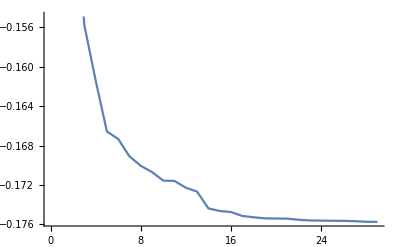

```mathematica
(* To test method, make sure it converges to expected values for given inputs *)
testplot=Gsconv[1,0.3,10];
ListLinePlot[testplot]
```